## Initilization

```mathematica
i=ImageResize[-Graphics-,500];
```

```mathematica
generateFrames[rule_Integer,steps_Integer:700,size_Integer:100,i_:i]:=ColorNegate@*Image/@CellularAutomaton[{rule,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{ImageData[ImagePad[ColorNegate[Binarize[ImageResize[i,size]]],10,Black]],0},steps]
```

## 01

```mathematica
frames=generateFrames[256576,700];
```

```mathematica
Manipulate[Show[frames[[n]],ImageSize->750],{n,1,Length@frames,1}]
```

Run the find new rules:

```mathematica
manyFrames=Table[rule->generateFrames[rule,100],{rule,RandomInteger[{(174826/2)-1000,(174826/2)+1000},16]*2}];
```

```mathematica
Manipulate[Thread[Labeled[manyFrames[[All,2,n]],manyFrames[[All,1]]]],{n,1,Length@manyFrames[[1,2]],1}]
```

```mathematica
manyFrames=Table[rule->generateFrames[rule,100],{rule,RandomInteger[{1,262142/2},100]*2}];
```

```mathematica
selectedFrames=Select[manyFrames,Function[association,Function[{rule,frames},
frames[[-1]]=!=frames[[-2]]&&
(Times@@ImageDimensions[frames[[-1]]]<80000)&&
(EuclideanDistance@@BorderDimensions[frames[[-1]]]<EuclideanDistance@@BorderDimensions[frames[[1]]])
][association[[1]],association[[2]]]]];
```

```mathematica
Manipulate[Thread[Labeled[selectedFrames[[All,2,n]],selectedFrames[[All,1]]]],{n,1,Length@manyFrames[[1,2]],1}]
```

Run to test a rule:

```mathematica
frames=generateFrames[175164,700];
```

$Aborted

```mathematica
Manipulate[Show[frames[[n]],ImageSize->750],{n,1,Length@frames,1}]
```

```mathematica
goodRules={174826,174688,174794,175164,175950,176510,175780,192184,175622,176632,47808,207594,256576};
```

```mathematica
SetDirectory[NotebookDirectory[]];
ParallelMap[Export[ToString[#]<>".gif",generateFrames[#],"DisplayDurations"->1/60]&,goodRules]
```

$Aborted

```mathematica
rule=174826;
```

```mathematica
frames=generateFrames[rule,1500];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export[ToString[rule]<>".mov",frames,Background->Transparent,"FrameRate"->60]
```

174826.mov

```mathematica
image3d=(Image3D[#,ImageSize->1000]&)@Map[ColorNegate]@Downsample[frames,5];
```

```mathematica
Last@Image3DSlices@ImageRotate[image3d,{t,{1,0,0}}]
```

```mathematica
image3d=Image3D[RandomReal[1,{5,10,10}]]
```

-Graphics3D-

```mathematica
Table[(#[[Round[Length[#]/2]]]&)@Image3DSlices@ImageRotate[image3d,{t,{1,0,0}}],{t,0,Pi/2,(Pi-(Pi/2))/5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Things to show

```mathematica
goodRules={174826,174688,174794,175164,175950,176510,175780,192184,175622,176632,47808,207594,256576};
```

```mathematica
frames=generateFrames[goodRules[[1]],700];
```

```mathematica
frames=generateFrames[goodRules[[2]],700];
```

```mathematica
frames=generateFrames[goodRules[[3]],700];
```

```mathematica
frames=generateFrames[goodRules[[4]],250];
```

```mathematica
frames=generateFrames[goodRules[[5]],250];
```

```mathematica
frames=generateFrames[goodRules[[6]],250];
```

```mathematica
frames=generateFrames[goodRules[[7]],250];
```

```mathematica
frames=generateFrames[goodRules[[8]],250];
```

```mathematica
frames=generateFrames[goodRules[[9]],250];
```

```mathematica
frames=generateFrames[goodRules[[10]],250];
```

```mathematica
frames=generateFrames[goodRules[[11]],700];
```

```mathematica
frames=generateFrames[goodRules[[12]],700];
```

```mathematica
frames=generateFrames[goodRules[[13]],1500];
```

```mathematica
Manipulate[Show[frames[[n]],ImageSize->750],{n,1,Length@frames,1}]
```

```mathematica
frame=-Graphics-;
```

```mathematica
logogramDirectory="~/Dropbox/SOYL/ReceivedMaterial/HiRez Logograms/Final Scripted Logograms/ScriptLogoJpegs/";
i2=(SetAlphaChannel[#,ColorNegate@#]&)/@(ImageResize[#,50]&)/@Import/@(logogramDirectory<>#&)/@Select[StringMatchQ[#,___~~".jpg"]&]@Import@logogramDirectory;
```

```mathematica
g=MorphologicalGraph[ImageCrop[ImagePad[ColorNegate@frame,{{30,0},{0,50}},Black],{100,100}]];
```

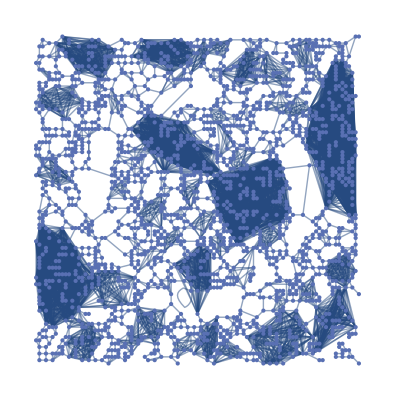

```mathematica
g
```

```mathematica
g2=MorphologicalGraph[ImageCrop[ImagePad[ColorNegate@frame,{{30,0},{0,50}},Black],{70,70}]];
```

```mathematica
graphFrame=Image[Graph[g2,VertexSize->1,VertexShape->(#->RandomChoice[i2]&/@VertexList[g2]),EdgeStyle->Directive[Opacity[0.7],Thickness[0.0002],Black],ImageSize->4096*2]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["graph-05.jpg",graphFrame]
```

graph-05.jpg

```mathematica
VertexShape->(#->RandomChoice[i2]&/@VertexList[g][[1;;10]])
```

```mathematica
Graph[g,VertexSize->1,EdgeStyle->Directive[Black,Thickness[.01]],VertexShape->(#->RandomChoice[i2]&/@VertexList[g][[1;;10]])]
```